# FUNCTIONS

```mathematica
colors={RGBColor[0.863, 0.133, 0.196],RGBColor[0.17600000000000002, 0.41600000000000004, 0.631],RGBColor[0.9690000000000001, 0.6859999999999999, 0.20800000000000002],RGBColor[0.349, Rational[7, 10], 0.33299999999999996],RGBColor[1, 0.5, 0],RGBColor[0.557, 0.573, 0.569]};
GetColor[deg_]:=Module[{},
Which[
deg ==1, colors⟦1⟧,
deg==2,colors⟦2⟧,
deg==3, colors⟦3⟧,
True, colors⟦6⟧
]
]
```

```mathematica
Boxpl[ac_,cv_,var_,title_] := Module[{},BoxWhiskerChart[{ac,cv,var},"Notched",
ChartStyle->Gray,ChartElementFunction->cef,
Frame->True,
(*FrameStyle->Black,*)
FrameTicks->{{Range[0,1,0.2],None},{None,None}},
FrameTicksStyle->12,
LabelStyle->12,
ImageSize->300,
ChartLabels->{"AR1", "CV", "Var"},
FrameLabel->{"","early-warning score",""},
PlotLabel->title,
AspectRatio->1/GoldenRatio]]
```

```mathematica
SSvsEWpl[network_, medianEW_,title_]:=Module[{},SensorScore = SS⟦network⟧;
vertexDegree=Deg⟦network⟧;
n = Length@SensorScore;
degrees = Sort@DeleteDuplicates@vertexDegree;
deg = degrees⟦1⟧;
temp=Table[
pos = Position[vertexDegree,deg]//Flatten;
ListPlot[Thread[{medianEW⟦pos⟧, SensorScore⟦pos⟧}],
PlotRange->{{0-0.01,Max@medianEW+0.01},{-0.05,1}},
GridLines->{{},{Max@SensorScore}},
GridLinesStyle->Directive[Gray,Dashed],
PlotStyle->Directive[GetColor[deg], PointSize[0.04],Opacity[0.7]],
 FrameTicks->{{Range[0,1,0.2],None},{Range[0,Max@medianEW,0.05],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True
]
,{deg,degrees}];

temp2 = ListPlot[Thread[{medianEW, SensorScore}],
PlotRange->{{0-0.01,Max[medianEW]+.05},{-0.05,1}},
(*GridLines->{{},{Max@SensorScore}},*)
GridLinesStyle->Directive[Gray,Dashed],
AspectRatio->1/GoldenRatio,
ImageSize->300,
FrameTicks->{{Range[0,1,0.5],None},{Range[0,1,0.2],None}},
ScalingFunctions->{"Reverse",Identity},
Frame->True,
PlotLabel->title,
PlotStyle-> Directive[Black, PointSize[0.05],Opacity[1]],
FrameTicksStyle->12,
LabelStyle->12,
FrameLabel->{"mean CV-based early-warning score","sensor score",""}
];

temp3 = ListPlot[Thread[{medianEW, SensorScore}],
ScalingFunctions->{"Reverse",Identity},
PlotStyle-> Directive[White, PointSize[0.04],Opacity[1]]
];

Show[temp2,temp3,temp,
FrameTicksStyle->12
]]
```

```mathematica
cef={ChartElementData["BoxWhisker"][##],EdgeForm[],FaceForm[None],ChartElementData["PointDensity","PointStyle"->Directive[EdgeForm[Black],Opacity[.5],PointSize[.01],Lighter[Charting`ChartStyleInformation["Color"]]]][##]}&;
```

# Load data

```mathematica
SetDirectory[NotebookDirectory[]];
SS = Import["data_GeneralFigs/SSall.mx"];
Deg = Import["data_GeneralFigs/Degree.mx"];
SetDirectory[NotebookDirectory[]<>"data_FigS14/"];
EW02add = Table[Table[Import["M_SD_002_"<>ind<>"_reps_"<>ToString[rep]<>"add_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
EW02mult = Table[Table[Import["M_SD_002_"<>ind<>"_reps_"<>ToString[rep]<>"mult_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
EW09add = Table[Table[Import["M_SD_009_"<>ind<>"_reps_"<>ToString[rep]<>"add_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
EW09mult = Table[Table[Import["M_SD_009_"<>ind<>"_reps_"<>ToString[rep]<>"mult_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
EW11add = Table[Table[Import["M_SD_011_"<>ind<>"_reps_"<>ToString[rep]<>"add_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
EW11mult = Table[Table[Import["M_SD_011_"<>ind<>"_reps_"<>ToString[rep]<>"mult_ewV.csv","Table"]//Flatten,{rep,Range[20]}],{ind,{"ac","cv","var"}}];
MeanEW02mult=Table[Table[Mean@Transpose[EW02mult⟦ind⟧]⟦sp⟧,{sp,Range[Length@Transpose[EW02mult⟦ind⟧]]}],{ind,3}];
MeanEW09mult=Table[Table[Mean@Transpose[EW09mult⟦ind⟧]⟦sp⟧,{sp,Range[Length@Transpose[EW09mult⟦ind⟧]]}],{ind,3}];
MeanEW11mult=Table[Table[Mean@Transpose[EW11mult⟦ind⟧]⟦sp⟧,{sp,Range[Length@Transpose[EW11mult⟦ind⟧]]}],{ind,3}];
```

# Make plots

## MSD002

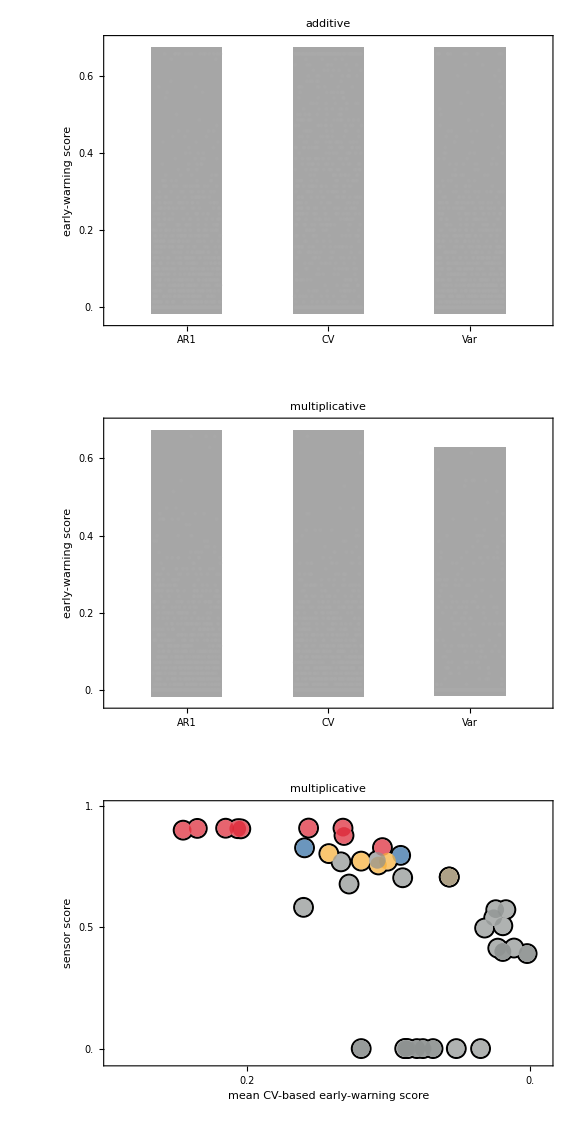

```mathematica
acadd=Flatten@EW02add⟦1⟧;
cvadd=Flatten@EW02add⟦2⟧;
varadd=Flatten@EW02add⟦3⟧;
acmult=Flatten@EW02mult⟦1⟧;
cvmult=Flatten@EW02mult⟦2⟧;
varmult=Flatten@EW02mult⟦3⟧;
GraphicsColumn[{Boxpl[acadd,cvadd,varadd,"additive"],Boxpl[acmult,cvmult,varmult,"multiplicative"],SSvsEWpl[2, MeanEW02mult⟦2⟧//Flatten,"multiplicative"]},ImageSize->Large]
```

# MSD009

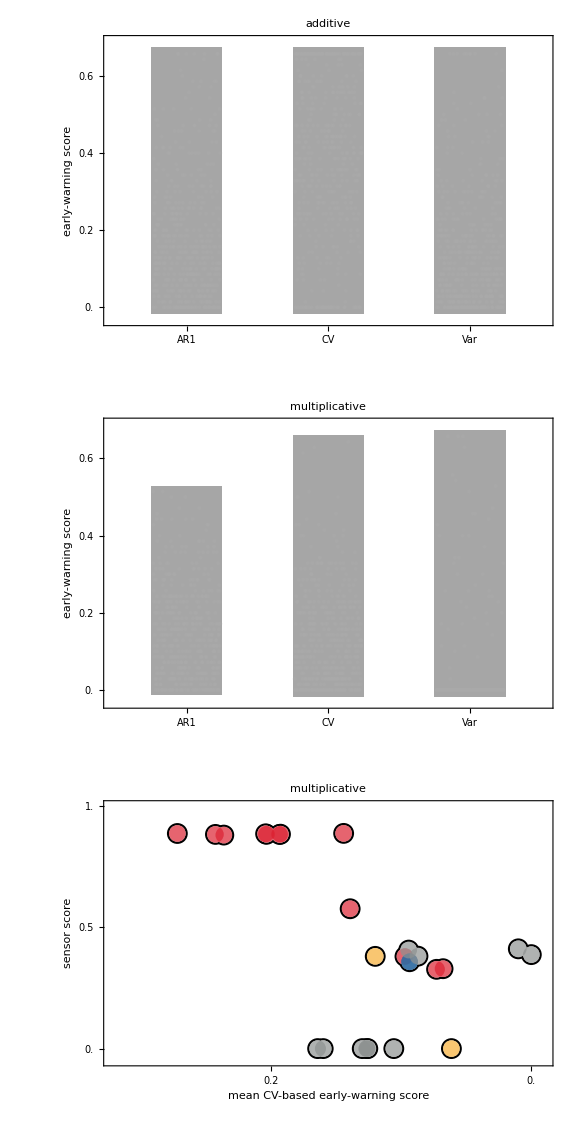

```mathematica
acadd=Flatten@EW09add⟦1⟧;
cvadd=Flatten@EW09add⟦2⟧;
varadd=Flatten@EW09add⟦3⟧;
acmult=Flatten@EW09mult⟦1⟧;
cvmult=Flatten@EW09mult⟦2⟧;
varmult=Flatten@EW09mult⟦3⟧;
GraphicsColumn[{Boxpl[acadd,cvadd,varadd,"additive"],Boxpl[acmult,cvmult,varmult,"multiplicative"],SSvsEWpl[5, MeanEW09mult⟦2⟧//Flatten,"multiplicative"]},ImageSize->Large]
```

# MSD011

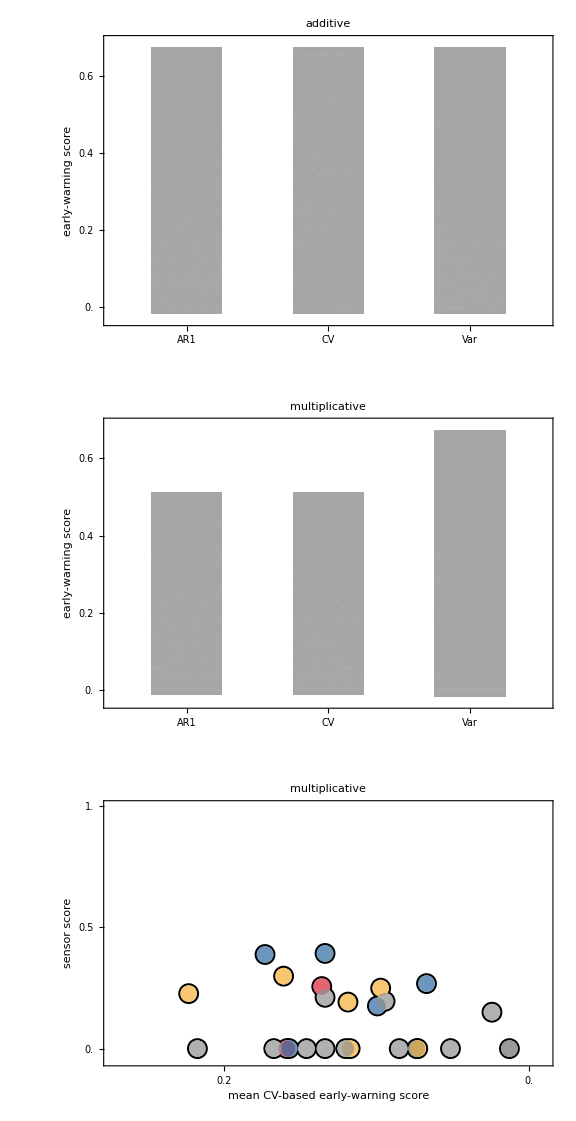

```mathematica
acadd=Flatten@EW11add⟦1⟧;
cvadd=Flatten@EW11add⟦2⟧;
varadd=Flatten@EW11add⟦3⟧;
acmult=Flatten@EW11mult⟦1⟧;
cvmult=Flatten@EW11mult⟦2⟧;
varmult=Flatten@EW11mult⟦3⟧;
GraphicsColumn[{Boxpl[acadd,cvadd,varadd,"additive"],Boxpl[acmult,cvmult,varmult,"multiplicative"],SSvsEWpl[6, MeanEW11mult⟦2⟧//Flatten,"multiplicative"]},ImageSize->Large]
```